# Sperm and pollen competition drive sex chromosome turnover

## Michael Scott & Matthew Osmond

This is much like van Doorn & Kirkpatrick 2007 (Nature 449:909), but with sperm/pollen competition as well (which we are hoping removes the need for sexually antagonistic selection to drive sex chromosome turnover).

## Resident life-cycle

We start with haploid selection, which occurs in sperm/pollen only. Let XAm be the frequency of allele A at the diallelic autosomal locus in gametes/pollen with an X allele at the diallelic sex-determining locus. Let YA be the frequency of allele A at the diallelic autosomal locus in gametes/pollen with an Y allele at the diallelic sex-determining locus. Let XAf be the frequency of allele A at the diallelic autosomal locus in eggs (which necessarily have an X allele at the diallelic sex-determining locus). After selection on male gametes/pollen we then have frequencies of A (and a) in each type of gamete/pollen:

```mathematica
wbarHap=(1-α)(wA XAm+wa Xam)+α(wA YA+wa Ya);
XAms=(1-α)wA XAm/wbarHap;
Xams=(1-α)wa Xam/wbarHap;
YAs=α wA*YA/wbarHap;
Yas=α wa*Ya/wbarHap;
XAfs=XAf;
Xafs=Xaf;
```

Check that frequencies A and a in each gamete/pollen type sum to one after selection:

```mathematica
1==XAms+Xams+YAs+Yas//Factor
1==XAfs+Xafs/.XAf->1-Xaf//Factor
```

True

True

After random mating, the frequencies of the diploid genotypes in each sex are

```mathematica
XAXA=XAfs XAms;
XAXa=XAfs Xams+Xafs XAms ;
XaXa=Xafs Xams;
XAYA=XAfs YAs;
XAYa=XAfs Yas;
XaYA=Xafs YAs;
XaYa=Xafs Yas;
```

Check that frequencies of diploid genotypes in each sex sum to one after mating:

```mathematica
(XAYA+XAYa+XaYA+XaYa)/(XAXA+XAXa+XaXa+XAYA+XAYa+XaYA+XaYa)/.wA->1/.wa->1/.Ya->1-YA/.Xam->1-XAm//Factor
```

α

After diploid selection (which can differ between males and females) the frequencies of the diploid genotypes in each sex are

```mathematica
wbarF=FAA XAXA+FAa XAXa+Faa XaXa;
wbarM=MAA XAYA+MAa XAYa+MAa XaYA+Maa XaYa;
XAXAs=FAA XAXA/wbarF;
XAXas=FAa XAXa/wbarF;
XaXas=Faa XaXa/wbarF;
XAYAs=MAA XAYA/wbarM;
XAYas=MAa XAYa/wbarM;
XaYAs=MAa XaYA/wbarM;
XaYas=Maa XaYa/wbarM;
```

Check that frequencies of diploid genotypes in each sex sum to one after diploid selection:

```mathematica
1==XAXAs+XAXas+XaXas//Factor
1==XAYAs+XAYas+XaYAs+XaYas//Factor
```

True

True

Finally, meiosis occurs, giving the haploid frequencies at the start of the next generation

```mathematica
XAfprime=XAXAs+XAXas/2;
Xafprime=XaXas+XAXas/2;
XAmprime=XAYAs+(1-r)XAYas+r XaYAs;
Xamprime=XaYas+r XAYas+(1-r) XaYAs;
YAprime=XAYAs+(1-r)XaYAs+ r XAYas;
Yaprime=XaYas+r XaYAs+(1- r) XAYas;
```

Check that frequencies of haploid genotypes sum to one after meiosis

```mathematica
1==XAfprime+Xafprime//Factor
1==XAmprime+Xamprime//Factor
1==YAprime+Yaprime//Factor
```

True

True

True

## Resident equilibrium

We now solve for the equilibrium frequency of A in each of the haploid genotypes. Equilibrium is achieved when the following three equations are zero

```mathematica
differenceEqs={
XAfprime-XAf,
XAmprime-XAm,
YAprime-YA
};
```

To simplify the analysis we assume weak selection in both haploids (sperm/pollen) and diploids

```mathematica
weaksel={
MAA->1+sAm ϵ,
MAa->1+hAm sAm ϵ,
Maa->1,
FAA->1+sAf ϵ,
FAa->1+hAf sAf ϵ,
Faa->1,
wA->1+t ϵ,
wa->1
};
```

We can write the frequencies as Taylor series

```mathematica
frequenciessub={
XAf->XAf0+XAf1 ϵ,
XAm->XAm0+XAm1 ϵ,
YA->YA0+YA1 ϵ
};
```

Without selection the recursions for the change in frequency of A in each gamete/pollen type are

```mathematica
differenceEqs0=Normal[Series[differenceEqs/.weaksel/.Xaf->1-XAf/.Ya->1-YA/.Xam->1-XAm/.frequenciessub,{ϵ,0,0}]]
```

{1/2 (-XAf0+XAm0),XAf0-r XAf0-XAm0+r YA0,r XAf0-r YA0}

And at equilibrium we have

```mathematica
sol0=Solve[recursions0==0,{XAf0,XAm0}]
```

{{XAf0→YA0,XAm0→YA0}}

So, with no selection, the equilibrium frequency of A in each gamete/pollen type is equal (and we call this pA).

Now, looking at only the first order selection terms, the recursions for the change in frequency of A in each gamete/pollen type are

```mathematica
differenceEqs1=Collect[Normal[Series[differenceEqs/.weaksel/.Xaf->1-XAf/.Ya->1-YA/.Xam->1-XAm/.frequenciessub/.sol0/.YA0->pA,{ϵ,0,1}]],ϵ,Factor]//Flatten
```

{1/2 (2 hAf pA sAf+2 pA^2 sAf-6 hAf pA^2 sAf-2 pA^3 sAf+4 hAf pA^3 sAf+pA t-pA^2 t-XAf1+XAm1) ϵ,(hAm pA sAm+pA^2 sAm-3 hAm pA^2 sAm-pA^3 sAm+2 hAm pA^3 sAm+pA r t-pA^2 r t+XAf1-r XAf1-XAm1+r YA1) ϵ,(hAm pA sAm+pA^2 sAm-3 hAm pA^2 sAm-pA^3 sAm+2 hAm pA^3 sAm+pA t-pA^2 t-pA r t+pA^2 r t+r XAf1-r YA1) ϵ}

Instead of solving for the first order genotype frequencies we will instead solve for the difference in the frequency of A in the different gamete/pollen types.

The difference in the frequency of A with X in females and X in males is (at equilibrium to first order in selection)

```mathematica
eqdpAXfXm=Solve[recursions1[[1]]==0/.XAf1->dpAXfXm+XAm1,dpAXfXm]//Flatten
```

{dpAXfXm→2 hAf pA sAf+2 pA^2 sAf-6 hAf pA^2 sAf-2 pA^3 sAf+4 hAf pA^3 sAf+pA t-pA^2 t}

The difference in the frequency of A with X in males and Y is (at equilibrium to first order in selection)

```mathematica
eqdpAXmY=Solve[recursions1[[2]]==0/.XAf1->dpAXfXm+XAm1/.eqdpAXfXm/.XAm1->dpAXmY+YA1,dpAXmY]//Flatten
```

{dpAXmY→1/r(2 hAf pA sAf+2 pA^2 sAf-6 hAf pA^2 sAf-2 pA^3 sAf+4 hAf pA^3 sAf-2 hAf pA r sAf-2 pA^2 r sAf+6 hAf pA^2 r sAf+2 pA^3 r sAf-4 hAf pA^3 r sAf+hAm pA sAm+pA^2 sAm-3 hAm pA^2 sAm-pA^3 sAm+2 hAm pA^3 sAm+pA t-pA^2 t)}

The difference in the frequency of A with X in females and Y is (at equilibrium to first order in selection)

```mathematica
eqdpAXfY=Solve[recursions1[[3]]==0/.XAf1->dpAXfY+YA1,dpAXfY]//Flatten
```

{dpAXfY→(-hAm pA sAm-pA^2 sAm+3 hAm pA^2 sAm+pA^3 sAm-2 hAm pA^3 sAm-pA t+pA^2 t+pA r t-pA^2 r t)/r}

So then, to first order, the equilibrium haploid genotype frequencies are(?)

```mathematica
eqXAf=XAf0+ϵ dpAXfXm+ϵ dpAXmY/.sol0/.YA0->pA/.eqdpAXfXm/.eqdpAXmY//Simplify
```

{(pA ((-1+pA) (2 hAf (-1+2 pA) sAf-hAm sAm-pA (2 sAf+sAm-2 hAm sAm)-t) ϵ+r (1+t (ϵ-pA ϵ))))/r}

```mathematica
eqXAm=XAm0-ϵ dpAXfXm+ϵ dpAXfY/.sol0/.YA0->pA/.eqdpAXfXm/.eqdpAXfY//Simplify
```

{(pA (-(-1+pA) (-pA sAm+hAm (-1+2 pA) sAm-t) ϵ+r (1-2 pA sAf ϵ+2 pA^2 sAf ϵ-2 hAf (1-3 pA+2 pA^2) sAf ϵ)))/r}

```mathematica
eqYA=YA0-ϵ dpAXfY+ϵ dpAXfXm/.sol0/.YA0->pA/.eqdpAXfY/.eqdpAXfXm//Simplify
```

{(pA ((-1+pA) (-pA sAm+hAm (-1+2 pA) sAm-t) ϵ+r (1+2 pA sAf ϵ-2 pA^2 sAf ϵ+2 hAf (1-3 pA+2 pA^2) sAf ϵ)))/r}

The change in the equilibrium frequency of A is

```mathematica
dpA=Collect[Normal[Series[2 XAfprime+XAmprime+YAprime-(2XAf-XAm-YA)/.weaksel/.Xaf->1-XAf/.Ya->1-YA/.Xam->1-XAm/.XAf->eqXAf/.XAm->eqXAm/.YA->eqYA,{ϵ,0,1}]]/4,ϵ,Simplify]//Flatten
```

{pA+1/2 (-1+pA) pA (hAf (-1+2 pA) sAf-hAm sAm-pA (sAf+sAm-2 hAm sAm)-t) ϵ}

And at equilibrium we have

```mathematica
eqpA=Solve[dpA-pA==0,pA]//FullSimplify
```

{{pA→0},{pA→1},{pA→-(hAf sAf+hAm sAm+t)/(sAf-2 hAf sAf+sAm-2 hAm sAm)}}

Notice that when t=0 we have equation “avgpASubs” in van Doorn & Kirkpatrick 2007 (SOM page 6). Sperm/pollen selection acts to increase the frequency of A (if selected for, t>0).

Notice that, without sperm/pollen competition, the non-trivial equilibrium does not exist when there is no sexually antagonistic selection

```mathematica
Reduce[(0<pA/.eqpA[[3]]/.t->0)&&(1>pA/.eqpA[[3]]/.t->0)&&sAm>0&&sAf>0&&hAf>0&&hAm>0&&hAf<1&&hAm<1,Reals]
```

False

```mathematica
Reduce[(0<pA/.eqpA[[3]]/.t->0)&&(1>pA/.eqpA[[3]]/.t->0)&&sAm<0&&sAf<0&&hAf>0&&hAm>0&&hAf<1&&hAm<1,Reals]
```

False

But with sperm/pollen competition it can exist, even without sexually antagonistic selection

```mathematica
Reduce[(0<pA/.eqpA[[3]])&&(1>pA/.eqpA[[3]])&&sAm<0&&sAf<0&&hAf>0&&hAm>0&&hAf<1&&hAm<1&&t>0,Reals]
```

sAm<0&&((sAf≤sAm&&0<hAm<1&&((0<hAf<(sAf+sAm-2 hAm sAm)/(2 sAf)&&-hAf sAf-hAm sAm<t<-sAf+hAf sAf-sAm+hAm sAm)||((sAf+sAm-2 hAm sAm)/(2 sAf)<hAf<1&&-sAf+hAf sAf-sAm+hAm sAm<t<-hAf sAf-hAm sAm)))||(sAm<sAf<0&&((0<hAm≤(-sAf+sAm)/(2 sAm)&&0<hAf<1&&-hAf sAf-hAm sAm<t<-sAf+hAf sAf-sAm+hAm sAm)||((-sAf+sAm)/(2 sAm)<hAm<(sAf+sAm)/(2 sAm)&&((0<hAf<(sAf+sAm-2 hAm sAm)/(2 sAf)&&-hAf sAf-hAm sAm<t<-sAf+hAf sAf-sAm+hAm sAm)||((sAf+sAm-2 hAm sAm)/(2 sAf)<hAf<1&&-sAf+hAf sAf-sAm+hAm sAm<t<-hAf sAf-hAm sAm)))||((sAf+sAm)/(2 sAm)≤hAm<1&&0<hAf<1&&-sAf+hAf sAf-sAm+hAm sAm<t<-hAf sAf-hAm sAm))))

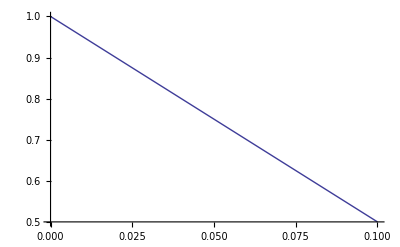

```mathematica
Plot[pA/.eqpA[[3]]/.sAf->-s/.sAm->-s/.hAf->h/.hAm->h/.s->1/10/.h->1,{t,0,1/10}]
```

## Can calculate equilibrium without weak selection with PAS (Fij=Mij=Wij) and r=1/2 (XAf=XAm=YA)

```mathematica
subPAS={FAA->WAA,FAa->WAa,Faa->Waa,MAA->WAA,MAa->WAa,Maa->Waa};
```

```mathematica
differenceEqsPAS={
XAfprime-XAf,
XAmprime-XAm,
YAprime-YA
}/.subPAS/.r->1/2;
```

```mathematica
subRes={Xaf->1-XAf,Xam->1-XAm,Ya->1-YA};
```

```mathematica
Solve[(differenceEqsPAS/.subRes)=={0,0,0},{XAf,XAm,YA}]
```

{{XAf→0,XAm→0,YA→0},{XAf→1,XAm→1,YA→1},{XAf→(2 wa Waa-wa WAa-wA WAa)/(2 (wa Waa-wa WAa-wA WAa+wA WAA)),XAm→(2 wa Waa-wa WAa-wA WAa)/(2 (wa Waa-wa WAa-wA WAa+wA WAA)),YA→(2 wa Waa-wa WAa-wA WAa)/(2 (wa Waa-wa WAa-wA WAa+wA WAA))}}

## Check (internal) Stability of Equilibrium

```mathematica
subRes={Xaf->1-XAf,Xam->1-XAm,Ya->1-YA};
```

```mathematica
matIntFull=Transpose[{D[{XAfprime,Xafprime,XAmprime,Xamprime,YAprime,Yaprime},XAf],
D[{XAfprime,Xafprime,XAmprime,Xamprime,YAprime,Yaprime},Xaf],
D[{XAfprime,Xafprime,XAmprime,Xamprime,YAprime,Yaprime},XAm],
D[{XAfprime,Xafprime,XAmprime,Xamprime,YAprime,Yaprime},Xam],
D[{XAfprime,Xafprime,XAmprime,Xamprime,YAprime,Yaprime},YA],
D[{XAfprime,Xafprime,XAmprime,Xamprime,YAprime,Yaprime},Ya]
}]/.subRes//Factor;
MatrixForm[%]
```

(-((-1+XAf) (Faa FAa wa^2-2 Faa FAa wa^2 XAm+2 Faa FAA wa wA XAm+Faa FAa wa^2 XAm^2-2 Faa FAA wa wA XAm^2+FAa FAA wA^2 XAm^2))/(2 (Faa wa-Faa wa XAf+FAa wa XAf-Faa wa XAm+FAa wA XAm+Faa wa XAf XAm-FAa wa XAf XAm-FAa wA XAf XAm+FAA wA XAf XAm)^2) | -(XAf (Faa FAa wa^2-2 Faa FAa wa^2 XAm+2 Faa FAA wa wA XAm+Faa FAa wa^2 XAm^2-2 Faa FAA wa wA XAm^2+FAa FAA wA^2 XAm^2))/(2 (Faa wa-Faa wa XAf+FAa wa XAf-Faa wa XAm+FAa wA XAm+Faa wa XAf XAm-FAa wa XAf XAm-FAa wA XAf XAm+FAA wA XAf XAm)^2) | (wa wA (-Faa FAa+2 Faa FAa XAf-2 Faa FAA XAf-Faa FAa XAf^2+2 Faa FAA XAf^2-FAa FAA XAf^2) (-1+XAm))/(2 (Faa wa-Faa wa XAf+FAa wa XAf-Faa wa XAm+FAa wA XAm+Faa wa XAf XAm-FAa wa XAf XAm-FAa wA XAf XAm+FAA wA XAf XAm)^2) | (wa wA (-Faa FAa+2 Faa FAa XAf-2 Faa FAA XAf-Faa FAa XAf^2+2 Faa FAA XAf^2-FAa FAA XAf^2) XAm)/(2 (Faa wa-Faa wa XAf+FAa wa XAf-Faa wa XAm+FAa wA XAm+Faa wa XAf XAm-FAa wa XAf XAm-FAa wA XAf XAm+FAA wA XAf XAm)^2) | 0 | 0
((-1+XAf) (Faa FAa wa^2-2 Faa FAa wa^2 XAm+2 Faa FAA wa wA XAm+Faa FAa wa^2 XAm^2-2 Faa FAA wa wA XAm^2+FAa FAA wA^2 XAm^2))/(2 (Faa wa-Faa wa XAf+FAa wa XAf-Faa wa XAm+FAa wA XAm+Faa wa XAf XAm-FAa wa XAf XAm-FAa wA XAf XAm+FAA wA XAf XAm)^2) | (XAf (Faa FAa wa^2-2 Faa FAa wa^2 XAm+2 Faa FAA wa wA XAm+Faa FAa wa^2 XAm^2-2 Faa FAA wa wA XAm^2+FAa FAA wA^2 XAm^2))/(2 (Faa wa-Faa wa XAf+FAa wa XAf-Faa wa XAm+FAa wA XAm+Faa wa XAf XAm-FAa wa XAf XAm-FAa wA XAf XAm+FAA wA XAf XAm)^2) | -(wa wA (-Faa FAa+2 Faa FAa XAf-2 Faa FAA XAf-Faa FAa XAf^2+2 Faa FAA XAf^2-FAa FAA XAf^2) (-1+XAm))/(2 (Faa wa-Faa wa XAf+FAa wa XAf-Faa wa XAm+FAa wA XAm+Faa wa XAf XAm-FAa wa XAf XAm-FAa wA XAf XAm+FAA wA XAf XAm)^2) | -(wa wA (-Faa FAa+2 Faa FAa XAf-2 Faa FAA XAf-Faa FAa XAf^2+2 Faa FAA XAf^2-FAa FAA XAf^2) XAm)/(2 (Faa wa-Faa wa XAf+FAa wa XAf-Faa wa XAm+FAa wA XAm+Faa wa XAf XAm-FAa wa XAf XAm-FAa wA XAf XAm+FAA wA XAf XAm)^2) | 0 | 0
-((-1+XAf) (Maa MAa wa^2-Maa MAa r wa^2-2 Maa MAa wa^2 YA+2 Maa MAa r wa^2 YA+MAa^2 wa wA YA+Maa MAA wa wA YA-2 MAa^2 r wa wA YA+Maa MAa wa^2 YA^2-Maa MAa r wa^2 YA^2-MAa^2 wa wA YA^2-Maa MAA wa wA YA^2+2 MAa^2 r wa wA YA^2+MAa MAA wA^2 YA^2-MAa MAA r wA^2 YA^2))/(-Maa wa+Maa wa XAf-MAa wa XAf+Maa wa YA-MAa wA YA-Maa wa XAf YA+MAa wa XAf YA+MAa wA XAf YA-MAA wA XAf YA)^2 | -(XAf (Maa MAa wa^2-Maa MAa r wa^2-2 Maa MAa wa^2 YA+2 Maa MAa r wa^2 YA+MAa^2 wa wA YA+Maa MAA wa wA YA-2 MAa^2 r wa wA YA+Maa MAa wa^2 YA^2-Maa MAa r wa^2 YA^2-MAa^2 wa wA YA^2-Maa MAA wa wA YA^2+2 MAa^2 r wa wA YA^2+MAa MAA wA^2 YA^2-MAa MAA r wA^2 YA^2))/(-Maa wa+Maa wa XAf-MAa wa XAf+Maa wa YA-MAa wA YA-Maa wa XAf YA+MAa wa XAf YA+MAa wA XAf YA-MAA wA XAf YA)^2 | 0 | 0 | (wa wA (-Maa MAa r+MAa^2 XAf-Maa MAA XAf+2 Maa MAa r XAf-2 MAa^2 r XAf-MAa^2 XAf^2+Maa MAA XAf^2-Maa MAa r XAf^2+2 MAa^2 r XAf^2-MAa MAA r XAf^2) (-1+YA))/(-Maa wa+Maa wa XAf-MAa wa XAf+Maa wa YA-MAa wA YA-Maa wa XAf YA+MAa wa XAf YA+MAa wA XAf YA-MAA wA XAf YA)^2 | (wa wA (-Maa MAa r+MAa^2 XAf-Maa MAA XAf+2 Maa MAa r XAf-2 MAa^2 r XAf-MAa^2 XAf^2+Maa MAA XAf^2-Maa MAa r XAf^2+2 MAa^2 r XAf^2-MAa MAA r XAf^2) YA)/(-Maa wa+Maa wa XAf-MAa wa XAf+Maa wa YA-MAa wA YA-Maa wa XAf YA+MAa wa XAf YA+MAa wA XAf YA-MAA wA XAf YA)^2
-((-1+XAf) (-Maa MAa wa^2+Maa MAa r wa^2+2 Maa MAa wa^2 YA-2 Maa MAa r wa^2 YA-MAa^2 wa wA YA-Maa MAA wa wA YA+2 MAa^2 r wa wA YA-Maa MAa wa^2 YA^2+Maa MAa r wa^2 YA^2+MAa^2 wa wA YA^2+Maa MAA wa wA YA^2-2 MAa^2 r wa wA YA^2-MAa MAA wA^2 YA^2+MAa MAA r wA^2 YA^2))/(Maa wa-Maa wa XAf+MAa wa XAf-Maa wa YA+MAa wA YA+Maa wa XAf YA-MAa wa XAf YA-MAa wA XAf YA+MAA wA XAf YA)^2 | -(XAf (-Maa MAa wa^2+Maa MAa r wa^2+2 Maa MAa wa^2 YA-2 Maa MAa r wa^2 YA-MAa^2 wa wA YA-Maa MAA wa wA YA+2 MAa^2 r wa wA YA-Maa MAa wa^2 YA^2+Maa MAa r wa^2 YA^2+MAa^2 wa wA YA^2+Maa MAA wa wA YA^2-2 MAa^2 r wa wA YA^2-MAa MAA wA^2 YA^2+MAa MAA r wA^2 YA^2))/(Maa wa-Maa wa XAf+MAa wa XAf-Maa wa YA+MAa wA YA+Maa wa XAf YA-MAa wa XAf YA-MAa wA XAf YA+MAA wA XAf YA)^2 | 0 | 0 | (wa wA (Maa MAa r-MAa^2 XAf+Maa MAA XAf-2 Maa MAa r XAf+2 MAa^2 r XAf+MAa^2 XAf^2-Maa MAA XAf^2+Maa MAa r XAf^2-2 MAa^2 r XAf^2+MAa MAA r XAf^2) (-1+YA))/(Maa wa-Maa wa XAf+MAa wa XAf-Maa wa YA+MAa wA YA+Maa wa XAf YA-MAa wa XAf YA-MAa wA XAf YA+MAA wA XAf YA)^2 | (wa wA (Maa MAa r-MAa^2 XAf+Maa MAA XAf-2 Maa MAa r XAf+2 MAa^2 r XAf+MAa^2 XAf^2-Maa MAA XAf^2+Maa MAa r XAf^2-2 MAa^2 r XAf^2+MAa MAA r XAf^2) YA)/(Maa wa-Maa wa XAf+MAa wa XAf-Maa wa YA+MAa wA YA+Maa wa XAf YA-MAa wa XAf YA-MAa wA XAf YA+MAA wA XAf YA)^2
((-1+XAf) (-Maa MAa r wa^2+2 Maa MAa r wa^2 YA+MAa^2 wa wA YA-Maa MAA wa wA YA-2 MAa^2 r wa wA YA-Maa MAa r wa^2 YA^2-MAa^2 wa wA YA^2+Maa MAA wa wA YA^2+2 MAa^2 r wa wA YA^2-MAa MAA r wA^2 YA^2))/(-Maa wa+Maa wa XAf-MAa wa XAf+Maa wa YA-MAa wA YA-Maa wa XAf YA+MAa wa XAf YA+MAa wA XAf YA-MAA wA XAf YA)^2 | (XAf (-Maa MAa r wa^2+2 Maa MAa r wa^2 YA+MAa^2 wa wA YA-Maa MAA wa wA YA-2 MAa^2 r wa wA YA-Maa MAa r wa^2 YA^2-MAa^2 wa wA YA^2+Maa MAA wa wA YA^2+2 MAa^2 r wa wA YA^2-MAa MAA r wA^2 YA^2))/(-Maa wa+Maa wa XAf-MAa wa XAf+Maa wa YA-MAa wA YA-Maa wa XAf YA+MAa wa XAf YA+MAa wA XAf YA-MAA wA XAf YA)^2 | 0 | 0 | -(wa wA (Maa MAa-Maa MAa r-2 Maa MAa XAf+MAa^2 XAf+Maa MAA XAf+2 Maa MAa r XAf-2 MAa^2 r XAf+Maa MAa XAf^2-MAa^2 XAf^2-Maa MAA XAf^2+MAa MAA XAf^2-Maa MAa r XAf^2+2 MAa^2 r XAf^2-MAa MAA r XAf^2) (-1+YA))/(-Maa wa+Maa wa XAf-MAa wa XAf+Maa wa YA-MAa wA YA-Maa wa XAf YA+MAa wa XAf YA+MAa wA XAf YA-MAA wA XAf YA)^2 | -(wa wA (Maa MAa-Maa MAa r-2 Maa MAa XAf+MAa^2 XAf+Maa MAA XAf+2 Maa MAa r XAf-2 MAa^2 r XAf+Maa MAa XAf^2-MAa^2 XAf^2-Maa MAA XAf^2+MAa MAA XAf^2-Maa MAa r XAf^2+2 MAa^2 r XAf^2-MAa MAA r XAf^2) YA)/(-Maa wa+Maa wa XAf-MAa wa XAf+Maa wa YA-MAa wA YA-Maa wa XAf YA+MAa wa XAf YA+MAa wA XAf YA-MAA wA XAf YA)^2
((-1+XAf) (Maa MAa r wa^2-2 Maa MAa r wa^2 YA-MAa^2 wa wA YA+Maa MAA wa wA YA+2 MAa^2 r wa wA YA+Maa MAa r wa^2 YA^2+MAa^2 wa wA YA^2-Maa MAA wa wA YA^2-2 MAa^2 r wa wA YA^2+MAa MAA r wA^2 YA^2))/(Maa wa-Maa wa XAf+MAa wa XAf-Maa wa YA+MAa wA YA+Maa wa XAf YA-MAa wa XAf YA-MAa wA XAf YA+MAA wA XAf YA)^2 | (XAf (Maa MAa r wa^2-2 Maa MAa r wa^2 YA-MAa^2 wa wA YA+Maa MAA wa wA YA+2 MAa^2 r wa wA YA+Maa MAa r wa^2 YA^2+MAa^2 wa wA YA^2-Maa MAA wa wA YA^2-2 MAa^2 r wa wA YA^2+MAa MAA r wA^2 YA^2))/(Maa wa-Maa wa XAf+MAa wa XAf-Maa wa YA+MAa wA YA+Maa wa XAf YA-MAa wa XAf YA-MAa wA XAf YA+MAA wA XAf YA)^2 | 0 | 0 | -(wa wA (-Maa MAa+Maa MAa r+2 Maa MAa XAf-MAa^2 XAf-Maa MAA XAf-2 Maa MAa r XAf+2 MAa^2 r XAf-Maa MAa XAf^2+MAa^2 XAf^2+Maa MAA XAf^2-MAa MAA XAf^2+Maa MAa r XAf^2-2 MAa^2 r XAf^2+MAa MAA r XAf^2) (-1+YA))/(Maa wa-Maa wa XAf+MAa wa XAf-Maa wa YA+MAa wA YA+Maa wa XAf YA-MAa wa XAf YA-MAa wA XAf YA+MAA wA XAf YA)^2 | -(wa wA (-Maa MAa+Maa MAa r+2 Maa MAa XAf-MAa^2 XAf-Maa MAA XAf-2 Maa MAa r XAf+2 MAa^2 r XAf-Maa MAa XAf^2+MAa^2 XAf^2+Maa MAA XAf^2-MAa MAA XAf^2+Maa MAa r XAf^2-2 MAa^2 r XAf^2+MAa MAA r XAf^2) YA)/(Maa wa-Maa wa XAf+MAa wa XAf-Maa wa YA+MAa wA YA+Maa wa XAf YA-MAa wa XAf YA-MAa wA XAf YA+MAA wA XAf YA)^2)

```mathematica
charpolyIntFull=Det[matIntFull-IdentityMatrix[6]*λ];
```

```mathematica
charpolyInt1=charpolyIntFull/.XAf->1/.XAm->1/.YA->1;
```

```mathematica
Normal[Series[charpolyInt1/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]
```

{{λ→0},{λ→0},{λ→0},{λ→1},{λ→1/4 (1-2 r-√(9-20 r+4 r^2))},{λ→1/4 (1-2 r+√(9-20 r+4 r^2))}}

```mathematica
Normal[Series[charpolyInt1/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
Solve[%==0,δλ1]
```

{{δλ1→1/2 (-sAf+hAf sAf-sAm+hAm sAm-t)}}

```mathematica
charpolyInt0=charpolyIntFull/.XAf->0/.XAm->0/.YA->0;
```

```mathematica
Normal[Series[charpolyInt0/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]
```

{{λ→0},{λ→0},{λ→0},{λ→1},{λ→1/4 (1-2 r-√(9-20 r+4 r^2))},{λ→1/4 (1-2 r+√(9-20 r+4 r^2))}}

```mathematica
Normal[Series[charpolyInt0/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
Solve[%==0,δλ1]
```

{{δλ1→1/2 (hAf sAf+hAm sAm+t)}}

So protected polymorphism requires that 
(-sAf(1-hAf) -sAm(1-hAm) - t ) > 0 && (hAf sAf + hAm sAm + t ) > 0

## Invasion of a neo-Y

Now assume there is a rare mutation at a new locus y, which is a dominant (over the X) masculinizing factor.

## Re-Write Recursions

We start with haploid selection, which occurs in sperm/pollen only. Let XAm be the frequency of allele A at the diallelic autosomal locus in gametes/pollen with an X allele at the diallelic sex-determining locus. Let YA be the frequency of allele A at the diallelic autosomal locus in gametes/pollen with an Y allele at the diallelic sex-determining locus. Let XAf be the frequency of allele A at the diallelic autosomal locus in eggs (which necessarily have an X allele at the diallelic sex-determining locus). After selection on male gametes/pollen we then have frequencies of A (and a) in each type of gamete/pollen:

XAm = pollen/sperm w/ XAy0
XAym= pollen/sperm w/ XAy1

```mathematica
wbarHap=(wA XAm+wa Xam+wA XAym+wa Xaym)+(wA YA+wa Ya+wA YAy+wa Yay);
XAms=wA XAm/wbarHap;
Xams=wa Xam/wbarHap;
XAyms=wA XAym/wbarHap;
Xayms=wa Xaym/wbarHap;
YAs= wA*YA/wbarHap;
Yas= wa*Ya/wbarHap;
YAys= wA*YAy/wbarHap;
Yays= wa*Yay/wbarHap;
XAfs=XAf;
Xafs=Xaf;
XAyfs=XAyf;
Xayfs=Xayf;
```

Check that frequencies A and a in each gamete/pollen type sum to one after selection:

```mathematica
1==XAms+Xams+YAs+Yas+XAyms+Xayms+YAys+Yays//Factor
1==XAfs+Xafs+XAyfs+Xayfs//Factor
```

True

1==Xaf+XAf+Xayf+XAyf

After random mating, the frequencies of the diploid genotypes in each sex are

```mathematica
XAXA=XAfs XAms;
XAXa=XAfs Xams+Xafs XAms ;
XaXa=Xafs Xams;
```

XX males (with a y)

```mathematica
XAyXA=XAyfs XAms+XAfs XAyms;
XAyXa=XAyfs Xams+Xafs XAyms ;
XAXay=XAfs Xayms+Xayfs XAms;
XayXa=Xayfs Xams+Xafs Xayms;
XAyXAy=XAyfs XAyms;
XAyXay=XAyfs Xayms+Xayfs XAyms ;
XayXay=Xayfs Xayms;
```

All other male types (can also carry y)

```mathematica
XAYA=XAfs YAs;
XAYa=XAfs Yas;
XaYA=Xafs YAs;
XaYa=Xafs Yas;

XAyYA=XAyfs YAs;
XAyYa=XAyfs Yas;
XayYA=Xayfs YAs;
XayYa=Xayfs Yas;

XAYAy=XAfs YAys;
XAYay=XAfs Yays;
XaYAy=Xafs YAys;
XaYay=Xafs Yays;

XAyYAy=XAyfs YAys;
XAyYay=XAyfs Yays;
XayYAy=Xayfs YAys;
XayYay=Xayfs Yays;
```

After diploid selection (which can differ between males and females) the frequencies of the diploid genotypes in each sex are

```mathematica
wbarF=FAA XAXA+FAa XAXa+Faa XaXa;
XAXAs=FAA XAXA/wbarF;
XAXas=FAa XAXa/wbarF;
XaXas=Faa XaXa/wbarF;

wbarM=
MAA XAyXA+MAa(XAyXa+XAXay)+Maa XayXa+
MAA XAyXAy+MAa XAyXay+Maa XayXay+
MAA XAYA+MAa (XAYa+XaYA)+Maa XaYa+
MAA XAyYA+MAa(XAyYa+XayYA)+Maa XayYa+
MAA XAYAy+MAa(XAYay+XaYAy)+Maa XaYay+
MAA XAyYAy+MAa(XAyYay+XayYAy)+Maa XayYay;
(*the XY males*)
XAYAs=MAA XAYA/wbarM;
XAYas=MAa XAYa/wbarM;
XaYAs=MAa XaYA/wbarM;
XaYas=Maa XaYa/wbarM;
(*XYy males that would have been males anyway*)
XAyYAs=MAA XAyYA/wbarM;
XAyYas=MAa XAyYa/wbarM;
XayYAs=MAa XayYA/wbarM;
XayYas=Maa XayYa/wbarM;

XAYAys=MAA XAYAy/wbarM;
XAYays=MAa XAYay/wbarM;
XaYAys=MAa XaYAy/wbarM;
XaYays=Maa XaYay/wbarM;

XAyYAys=MAA XAyYAy/wbarM;
XAyYays=MAa XAyYay/wbarM;
XayYAys=MAa XayYAy/wbarM;
XayYays=Maa XayYay/wbarM;
(*the XXy males, extra males created by neoY*)
XAyXAs=MAA XAyXA/wbarM;
XAyXas=MAa XAyXa/wbarM;
XAXays=MAa XAXay/wbarM;
XayXas=Maa XayXa/wbarM;

XAyXAys=MAA XAyXAy/wbarM;
XAyXays=MAa XAyXay/wbarM;
XayXays=Maa XayXay/wbarM;
```

Check that frequencies of diploid genotypes in each sex sum to one after diploid selection:

```mathematica
1==XAXAs+XAXas+XaXas//Factor
1==(XAyXAs+XAyXas+XAXays+XayXas+
XAyXAys+XAyXays+XayXays+
XAYAs+XAYas+XaYAs+XaYas+
XAyYAs+XAyYas+XayYAs+XayYas+
XAYAys+XAYays+XaYAys+XaYays+
XAyYAys+XAyYays+XayYAys+XayYays)//Factor
```

True

True

NOTICE THAT, the frequency of all males after diploid selection sums to 1. There are both XX (with y) and XY males. For this reason I’m not sure we can make the frequencies of X and Y pollen/sperm both sum to 1. Rather, I changed the pollen/sperm production so that the total of X and Y pollen/sperm sum to 1.

Finally, meiosis occurs, giving the haploid frequencies at the start of the next generation

Next, eggs/ovules are produced by females.

```mathematica
XAfprime=XAXAs+XAXas/2;
Xafprime=XaXas+XAXas/2;
```

```mathematica
1==XAfprime+Xafprime//Factor
```

True

NOTE: I have put the α (fraction of Y pollen/sperm produced by a male here)

r is the recombination rate between A and Y
R is the recombination rate between y and A
χ is the recombination rate between y and Y

```mathematica
XAmprime =(1-α)(XAYAs+(XAYas(1-r)+XaYAs (r))+
(XAYAys(1-(r+R-2χ))+XAyYAs (r+R-2χ))+
(XAYays (1-(r+R-χ))+XayYAs(r-χ)+XaYAys(χ)+XAyYas(R-χ)))+
(XAyXAs/2+XAyXas R/2+XAXays (1-R)/2);
Xamprime =(1-α)(XaYas+(XAYas(r)+XaYAs (1-r))+
(XaYays (1-(r+R-2χ))+XayYas(r+R-2χ))+
(XAYays(χ)+XayYAs(R-χ)+XaYAys(1-(r+R-χ))+XAyYas(r-χ)))+
(XayXas/2 +XAyXas (1-R)/2+XAXays (R)/2);
XAymprime =(1-α)(XAyYAys+(XAyYays(1-r)+XayYAys(r))+
(XAYAys(r+R-2χ)+XAyYAs(1-(r+R-2χ)))+
(XAYays(R-χ)+XayYAs(χ)+XaYAys(r-χ)+XAyYas (1-(r+R-χ))))+
(XAyXAs/2+XAyXas (1-R)/2+XAXays (R)/2+XAyXAys+XAyXays/2);
Xaymprime =(1-α)(XayYays+(XAyYays(r)+XayYAys(1-r))+
(XaYays (r+R-2χ)+XayYas(1-(r+R-2χ)))+
(XAYays(r-χ)+XayYAs(1-(r+R-χ))+XaYAys(R-χ)+XAyYas (χ)))+
(XayXas/2 +XAyXas (R)/2+XAXays (1-R)/2+XayXays+XAyXays/2);

YAprime =α(XAYAs+(XAYas(r)+XaYAs (1-r))+
(XAYAys(r+R-2χ)+XAyYAs (1-(r+R-2χ)))+
(XAYays (r-χ)+XayYAs(1-(r+R-χ))+XaYAys(R-χ)+XAyYas(χ)));
Yaprime=α(XaYas+(XAYas(1-r)+XaYAs (r))+
(XaYays (r+R-2χ)+XayYas (1-(r+R-2χ)))+
(XAYays(R-χ)+XayYAs(χ)+XaYAys(r-χ)+XAyYas (1-(r+R-χ))));
YAyprime =α(XAyYAys+(XAyYays(r)+XayYAys(1-r))+
(XAYAys(1-(r+R-2χ))+XAyYAs(r+R-2χ))+
(XAYays (χ)+XayYAs(R-χ)+XaYAys(1-(r+R-χ))+XAyYas (r-χ)));
Yayprime =α(XayYays+(XAyYays(1-r)+XayYAys(r))+
(XaYays(1-(r+R-2χ))+XayYas(r+R-2χ))+
(XAYays(1-(r+R-χ))+XayYAs(r-χ)+XaYAys(χ)+XAyYas(R-χ)));
```

```mathematica
Factor[XAmprime+Xamprime+XAymprime+Xaymprime+YAprime+Yaprime+YAyprime+Yayprime]
```

1

Which might be easier to look at in this form:

First, we write use the following terms, which will then allow us to choose different gene orders and different degrees of cross-over interference. 
* RX is the chance of a double recombinant 
* RA is the chance of either one or two recombination events in a triple heterozygote
* RO is the chance of exactly one recombination event separating y and Y
* R1 is the chance of only a recombination event between y and A
* R2 is the chance of only a recombination event between A and the Y

```mathematica
subR={RA->r+Rm-χ,R0->r+Rm-2χ,R1->Rm-χ,R2->r-χ};
```

```mathematica
XAmprime =(1-α)(XAYAs+(XAYas(1-r)+XaYAs (r))+
(XAYAys(1-R0)+XAyYAs (R0))+
(XAYays (1-RA)+XayYAs(R2)+XaYAys(RX)+XAyYas(R1)))+
(XAyXAs/2+XAyXas R/2+XAXays (1-R)/2);
Xamprime =(1-α)(XaYas+(XAYas(r)+XaYAs (1-r))+
(XaYays (1-R0)+XayYas(R0))+
(XAYays(RX)+XayYAs(R1)+XaYAys(1-RA)+XAyYas(R2)))+
(XayXas/2 +XAyXas (1-R)/2+XAXays (R)/2);
XAymprime =(1-α)(XAyYAys+(XAyYays(1-r)+XayYAys(r))+
(XAYAys(R0)+XAyYAs(1-R0))+
(XAYays(R1)+XayYAs(RX)+XaYAys(R2)+XAyYas (1-RA)))+
(XAyXAs/2+XAyXas (1-R)/2+XAXays (R)/2+XAyXAys+XAyXays/2);
Xaymprime =(1-α)(XayYays+(XAyYays(r)+XayYAys(1-r))+
(XaYays (R0)+XayYas(1-R0))+
(XAYays(R2)+XayYAs(1-RA)+XaYAys(R1)+XAyYas (RX)))+
(XayXas/2 +XAyXas (R)/2+XAXays (1-R)/2+XayXays+XAyXays/2);

YAprime =α(XAYAs+(XAYas(r)+XaYAs (1-r))+
(XAYAys(R0)+XAyYAs (1-R0))+
(XAYays (R2)+XayYAs(1-RA)+XaYAys(R1)+XAyYas(RX)));
Yaprime=α(XaYas+(XAYas(1-r)+XaYAs (r))+
(XaYays (R0)+XayYas (1-R0))+
(XAYays(R1)+XayYAs(RX)+XaYAys(R2)+XAyYas (1-RA)));
YAyprime =α(XAyYAys+(XAyYays(r)+XayYAys(1-r))+
(XAYAys(1-R0)+XAyYAs(R0))+
(XAYays (RX)+XayYAs(R1)+XaYAys(1-RA)+XAyYas (R2)));
Yayprime =α(XayYays+(XAyYays(1-r)+XayYAys(r))+
(XaYays(1-R0)+XayYas(R0))+
(XAYays(1-RA)+XayYAs(R2)+XaYAys(RX)+XAyYas(R1)));
```

```mathematica
Factor[XAmprime+Xamprime+XAymprime+Xaymprime+YAprime+Yaprime+YAyprime+Yayprime/.subR]
```

(Maa wa Xam Xayf+MAa wA XAm Xayf+MAa wa Xam XAyf+MAA wA XAm XAyf+Maa wa Xaf Xaym+MAa wa XAf Xaym+Maa wa Xayf Xaym+MAa wa XAyf Xaym+MAa wA Xaf XAym+MAA wA XAf XAym+MAa wA Xayf XAym+MAA wA XAyf XAym+Maa wa Xaf Ya+MAa wa XAf Ya+Maa wa Xayf Ya+MAa wa XAyf Ya+MAa RX wa XAyf Ya+MAa wA Xaf YA+MAA wA XAf YA+MAa wA Xayf YA+MAa RX wA Xayf YA+MAA wA XAyf YA+Maa wa Xaf Yay+MAa wa XAf Yay+MAa RX wa XAf Yay+Maa wa Xayf Yay+MAa wa XAyf Yay+MAa wA Xaf YAy+MAa RX wA Xaf YAy+MAA wA XAf YAy+MAa wA Xayf YAy+MAA wA XAyf YAy-MAa wa XAyf Ya χ-MAa wA Xayf YA χ-MAa wa XAf Yay χ-MAa wA Xaf YAy χ)/(Maa wa Xam Xayf+MAa wA XAm Xayf+MAa wa Xam XAyf+MAA wA XAm XAyf+Maa wa Xaf Xaym+MAa wa XAf Xaym+Maa wa Xayf Xaym+MAa wa XAyf Xaym+MAa wA Xaf XAym+MAA wA XAf XAym+MAa wA Xayf XAym+MAA wA XAyf XAym+Maa wa Xaf Ya+MAa wa XAf Ya+Maa wa Xayf Ya+MAa wa XAyf Ya+MAa wA Xaf YA+MAA wA XAf YA+MAa wA Xayf YA+MAA wA XAyf YA+Maa wa Xaf Yay+MAa wa XAf Yay+Maa wa Xayf Yay+MAa wa XAyf Yay+MAa wA Xaf YAy+MAA wA XAf YAy+MAa wA Xayf YAy+MAA wA XAyf YAy)

## Resident equilibrium (new recursions - adjusted for the new position of α)

We will assume that the neoY is absent

```mathematica
subequil={
XAf->pXf,
Xaf->(1-pXf),
XAm->pXm(1-α),
Xam->(1-pXm)(1-α),
YA->pY*α,
Ya->(1-pY)*α,
XAyf->0,
Xayf->0,
XAym->0,
Xaym->0,
YAy->0,
Yay->0
};
```

We now solve for the equilibrium frequency of A in each of the haploid genotypes. Equilibrium is achieved when the following three equations are zero

```mathematica
differenceEqs={
XAfprime-XAf,
XAmprime-XAm,
YAprime-YA
}/.subequil;
```

To simplify the analysis we assume weak selection in both haploids (sperm/pollen) and diploids

```mathematica
weaksel={
MAA->1+sAm ϵ,
MAa->1+hAm sAm ϵ,
Maa->1,
FAA->1+sAf ϵ,
FAa->1+hAf sAf ϵ,
Faa->1,
wA->1+t ϵ,
wa->1
};
```

We can write the frequencies as Taylor series

```mathematica
frequenciessub={
pXf->pXf0+pXf1 ϵ,
pXm->pXm0+pXm1 ϵ,
pY->pY0+pY1 ϵ
};
```

Without selection the recursions for the change in frequency of A in each gamete/pollen type are

```mathematica
differenceEqs0=Normal[Series[differenceEqs/.weaksel/.frequenciessub,{ϵ,0,0}]]
```

{1/2 (-pXf0+pXm0),-pXm0+(pXf0-pXf0 r+pY0 r) (1-α)+pXm0 α,pXf0 r α-pY0 r α}

And at equilibrium we have

```mathematica
sol0=Solve[differenceEqs0==0,{pXf0,pXm0}]
```

{{pXf0→pY0,pXm0→pY0}}

So, with no selection, the equilibrium frequency of A in each gamete/pollen type is equal (and we call this pA).

Now, looking at only the first order selection terms, the recursions for the change in frequency of A in each gamete/pollen type are

```mathematica
differenceEqs1=Collect[Normal[Series[differenceEqs/.weaksel/.frequenciessub/.sol0,{ϵ,0,1}]],ϵ,Factor]/.pY0->pA//Flatten
```

{1/2 (-pXf1+pXm1+2 hAf pA sAf+2 pA^2 sAf-6 hAf pA^2 sAf-2 pA^3 sAf+4 hAf pA^3 sAf+pA t-pA^2 t) ϵ,(-pXf1+pXm1+pXf1 r-pY1 r-hAm pA sAm-pA^2 sAm+3 hAm pA^2 sAm+pA^3 sAm-2 hAm pA^3 sAm-pA r t+pA^2 r t) (-1+α) ϵ,(pXf1 r-pY1 r+hAm pA sAm+pA^2 sAm-3 hAm pA^2 sAm-pA^3 sAm+2 hAm pA^3 sAm+pA t-pA^2 t-pA r t+pA^2 r t) α ϵ}

```mathematica
Solve[differenceEqs1==0,{pXf1,pXm1,pY1}]
```

{}

Instead of solving for the first order genotype frequencies we will instead solve for the difference in the frequency of A in the different gamete/pollen types.

The difference in the frequency of A with X in females and X in males is (at equilibrium to first order in selection)

```mathematica
eqdpAXfXm=Solve[differenceEqs1[[1]]==0/.pXf1->dpAXfXm+pXm1,dpAXfXm]//Flatten
```

{dpAXfXm→2 hAf pA sAf+2 pA^2 sAf-6 hAf pA^2 sAf-2 pA^3 sAf+4 hAf pA^3 sAf+pA t-pA^2 t}

The difference in the frequency of A with X in males and Y is (at equilibrium to first order in selection)

```mathematica
eqdpAXmY=Solve[differenceEqs1[[2]]==0/.pXf1->dpAXfXm+pXm1/.eqdpAXfXm/.pXm1->dpAXmY+pY1,dpAXmY]//Flatten
```

{dpAXmY→1/r(2 hAf pA sAf+2 pA^2 sAf-6 hAf pA^2 sAf-2 pA^3 sAf+4 hAf pA^3 sAf-2 hAf pA r sAf-2 pA^2 r sAf+6 hAf pA^2 r sAf+2 pA^3 r sAf-4 hAf pA^3 r sAf+hAm pA sAm+pA^2 sAm-3 hAm pA^2 sAm-pA^3 sAm+2 hAm pA^3 sAm+pA t-pA^2 t)}

The difference in the frequency of A with X in females and Y is (at equilibrium to first order in selection)

```mathematica
eqdpAXfY=Solve[differenceEqs1[[3]]==0/.pXf1->dpAXfY+pY1,dpAXfY]//Flatten
```

{dpAXfY→(-hAm pA sAm-pA^2 sAm+3 hAm pA^2 sAm+pA^3 sAm-2 hAm pA^3 sAm-pA t+pA^2 t+pA r t-pA^2 r t)/r}

So then, to first order, the equilibrium haploid genotype frequencies are(?)

```mathematica
eqpXf=pXf0+ϵ dpAXfXm+ϵ dpAXmY/.sol0/.pY0->pA/.eqdpAXfXm/.eqdpAXmY//Simplify
```

{(pA ((-1+pA) (2 hAf (-1+2 pA) sAf-hAm sAm-pA (2 sAf+sAm-2 hAm sAm)-t) ϵ+r (1+t (ϵ-pA ϵ))))/r}

```mathematica
eqpXm=pXm0-ϵ dpAXfXm+ϵ dpAXfY/.sol0/.pY0->pA/.eqdpAXfXm/.eqdpAXfY//Simplify
```

{(pA (-(-1+pA) (-pA sAm+hAm (-1+2 pA) sAm-t) ϵ+r (1-2 pA sAf ϵ+2 pA^2 sAf ϵ-2 hAf (1-3 pA+2 pA^2) sAf ϵ)))/r}

```mathematica
eqpY=pY0+ϵ dpAXfXm-ϵ dpAXfY/.sol0/.pY0->pA/.eqdpAXfY/.eqdpAXfXm//Simplify
```

{(pA ((-1+pA) (-pA sAm+hAm (-1+2 pA) sAm-t) ϵ+r (1+2 pA sAf ϵ-2 pA^2 sAf ϵ+2 hAf (1-3 pA+2 pA^2) sAf ϵ)))/r}

The recursion for pA is given by

```mathematica
dpA=Collect[Normal[Series[ 2XAfprime+XAmprime/(1-α)+YAprime/α-(2XAf-XAm/(1-α)-YA/α)/.weaksel/.subequil/.pXf->eqpXf/.pXm->eqpXm/.pY->eqpY,{ϵ,0,1}]]/4,ϵ,Simplify]/.ϵ->1//Flatten
```

{pA+1/2 (-1+pA) pA (hAf (-1+2 pA) sAf-hAm sAm-pA (sAf+sAm-2 hAm sAm)-t)}

And at equilibrium we have

```mathematica
Solve[dpA-pA==0,pA]
```

{{pA→0},{pA→1},{pA→(hAf sAf+hAm sAm+t)/(-sAf+2 hAf sAf-sAm+2 hAm sAm)}}

Notice that when t=0 we have equation “avgpASubs” in van Doorn & Kirkpatrick 2007 (SOM page 6). Sperm/pollen selection acts to increase the frequency of A (if selected for, t>0).

## Check (internal) Stability of Equilibrium (should be the same as above but need to adjust for α)

## External Stability (i.e., invasion of a neo Y)

```mathematica
subequil
```

{XAf→pXf,Xaf→1-pXf,XAm→pXm (1-α),Xam→(1-pXm) (1-α),YA→pY α,Ya→(1-pY) α,XAyf→0,Xayf→0,XAym→0,Xaym→0,YAy→0,Yay→0}

Notice that we don’t have recursions for XAyf or Xayf because y is a dominant male determining gene. However, we allowed these genotypes to create zygotes so we can include them in the stability matrix.

```mathematica
matExtFull=Transpose[{D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},XAyf],
D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},Xayf],
D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},XAym],
D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},Xaym],
D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},YAym],
D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},Yaym]
}]/.subequil//Factor;
MatrixForm[%]
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
((-1+α) (MAa wa-MAa pXm wa-MAa R wa+MAa pXm R wa+MAA pXm wA+2 MAa wa α-2 MAa pY wa α-2 MAa RA wa α+2 MAa pY RA wa α+2 MAA pY wA α-2 MAA pY R0 wA α))/(2 (-Maa wa+Maa pXf wa-MAa pXf wa+Maa pY wa-Maa pXf pY wa+MAa pXf pY wa-MAa pY wA+MAa pXf pY wA-MAA pXf pY wA) α) | (MAa wA (-1+α) (pXm R+2 pY RX α))/(2 (-Maa wa+Maa pXf wa-MAa pXf wa+Maa pY wa-Maa pXf pY wa+MAa pXf pY wa-MAa pY wA+MAa pXf pY wA-MAA pXf pY wA) α) | ((MAa-MAa pXf+MAA pXf-MAa R+MAa pXf R) wA)/(2 (Maa wa-Maa pXf wa+MAa pXf wa-Maa pY wa+Maa pXf pY wa-MAa pXf pY wa+MAa pY wA-MAa pXf pY wA+MAA pXf pY wA) α) | -(MAa pXf R wa)/(2 (-Maa wa+Maa pXf wa-MAa pXf wa+Maa pY wa-Maa pXf pY wa+MAa pXf pY wa-MAa pY wA+MAa pXf pY wA-MAA pXf pY wA) α) | 0 | 0
-(MAa wa (-1+α) (-R+pXm R-2 RX α+2 pY RX α))/(2 (-Maa wa+Maa pXf wa-MAa pXf wa+Maa pY wa-Maa pXf pY wa+MAa pXf pY wa-MAa pY wA+MAa pXf pY wA-MAA pXf pY wA) α) | ((-1+α) (-Maa wa+Maa pXm wa-MAa pXm wA+MAa pXm R wA-2 Maa wa α+2 Maa pY wa α+2 Maa R0 wa α-2 Maa pY R0 wa α-2 MAa pY wA α+2 MAa pY RA wA α))/(2 (Maa wa-Maa pXf wa+MAa pXf wa-Maa pY wa+Maa pXf pY wa-MAa pXf pY wa+MAa pY wA-MAa pXf pY wA+MAA pXf pY wA) α) | (MAa (-1+pXf) R wA)/(2 (-Maa wa+Maa pXf wa-MAa pXf wa+Maa pY wa-Maa pXf pY wa+MAa pXf pY wa-MAa pY wA+MAa pXf pY wA-MAA pXf pY wA) α) | -((-Maa+Maa pXf-MAa pXf+MAa pXf R) wa)/(2 (Maa wa-Maa pXf wa+MAa pXf wa-Maa pY wa+Maa pXf pY wa-MAa pXf pY wa+MAa pY wA-MAa pXf pY wA+MAA pXf pY wA) α) | 0 | 0
((-MAa R2 wa+MAa pY R2 wa-MAA pY R0 wA) α)/(-Maa wa+Maa pXf wa-MAa pXf wa+Maa pY wa-Maa pXf pY wa+MAa pXf pY wa-MAa pY wA+MAa pXf pY wA-MAA pXf pY wA) | -(MAa pY R1 wA α)/(-Maa wa+Maa pXf wa-MAa pXf wa+Maa pY wa-Maa pXf pY wa+MAa pXf pY wa-MAa pY wA+MAa pXf pY wA-MAA pXf pY wA) | 0 | 0 | 0 | 0
(MAa (-1+pY) R1 wa α)/(-Maa wa+Maa pXf wa-MAa pXf wa+Maa pY wa-Maa pXf pY wa+MAa pXf pY wa-MAa pY wA+MAa pXf pY wA-MAA pXf pY wA) | -((-Maa R0 wa+Maa pY R0 wa-MAa pY R2 wA) α)/(Maa wa-Maa pXf wa+MAa pXf wa-Maa pY wa+Maa pXf pY wa-MAa pXf pY wa+MAa pY wA-MAa pXf pY wA+MAA pXf pY wA) | 0 | 0 | 0 | 0)

```mathematica
charpolyExt=Det[matExtFull-IdentityMatrix[6]*λ];
```

```mathematica
Normal[Series[charpolyExt/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]
```

{{λ→0},{λ→0},{λ→0},{λ→0},{λ→1/(2 α)},{λ→(1-R)/(2 α)}}

It seems that Yy-bearing males have no effect on the invasion (would have been males anyway). The inclusion of Xiyf is also irrelevant as mutations arising in females are males in the next generation.

The first order effect is on sex ratio. If the initial population has a sex ratio bias (e.g., produces an excess of X-bearing pollen/sperm, α<1/2), then a male determiner will invade. I think an initial sex ratio bias selecting for neo sex determiners was discussed by Jim Bull ???

Here, we will assume that any deviations from α=1/2 are on the order of ϵ

```mathematica
Normal[Series[charpolyExt/.weaksel/.α->1/2+δα*ϵ,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]
```

{{λ→0},{λ→0},{λ→0},{λ→0},{λ→1},{λ→1-R}}

```mathematica
Normal[Series[charpolyExt/.weaksel/.α->1/2+δα*ϵ/.λ->1+δλ*ϵ/.frequenciessub/.sol0,{ϵ,0,1}]]//Factor;
Solve[%==0,δλ]
```

{{δλ→-2 δα}}

Going to the next order in ϵ (and assuming that δα is of order ϵ^2)

```mathematica
Normal[Series[charpolyExt/.weaksel/.α->1/2+δα*ϵ^2/.λ->1+δλ1*ϵ/.frequenciessub/.sol0,{ϵ,0,1}]]//Factor;
Solve[%==0,δλ1]
```

{{δλ1→0}}

```mathematica
Normal[Series[charpolyExt/.weaksel/.α->1/2+δα*ϵ^2/.λ->1+δλ2*ϵ^2/.frequenciessub/.sol0,{ϵ,0,2}]]//Factor;
Solve[%==0,δλ2]
```

{{δλ2→1/R(hAm pXf1 R sAm+pXf1 pY0 R sAm-2 hAm pXf1 pY0 R sAm-hAm pY1 R sAm-pY0 pY1 R sAm+2 hAm pY0 pY1 R sAm+hAm^2 pY0 sAm^2+2 hAm pY0^2 sAm^2-5 hAm^2 pY0^2 sAm^2+pY0^3 sAm^2-6 hAm pY0^3 sAm^2+8 hAm^2 pY0^3 sAm^2-pY0^4 sAm^2+4 hAm pY0^4 sAm^2-4 hAm^2 pY0^4 sAm^2+pXf1 R t-pY1 R t+2 hAm pY0 sAm t+2 pY0^2 sAm t-6 hAm pY0^2 sAm t-2 pY0^3 sAm t+4 hAm pY0^3 sAm t-hAm pY0 R sAm t-pY0^2 R sAm t+3 hAm pY0^2 R sAm t+pY0^3 R sAm t-2 hAm pY0^3 R sAm t+pY0 t^2-pY0^2 t^2-pY0 R t^2+pY0^2 R t^2-2 R δα)}}

```mathematica
frequenciessub
```

{pXf→pXf0+pXf1 ϵ,pXm→pXm0+pXm1 ϵ,pY→pY0+pY1 ϵ}

```mathematica
Normal[Series[charpolyExt/.weaksel/.α->1/2+δα*ϵ^2/.λ->1+δλ2*ϵ^2/.pXf->eqpXf/.pXm->eqpXm/.pY->eqpY,{ϵ,0,2}]]//Factor;
Solve[%==0,δλ2];
solδλ2=Collect[δλ2/.%,δα,Simplify]
```

{((-1+pA) pA (-pA sAm+hAm (-1+2 pA) sAm-t) (2 hAf (-1+2 pA) (-1+r) R sAf+pA (-2 (-1+r) R sAf+(1-2 hAm) r sAm)+r (hAm sAm+t)))/(r R)-2 δα}

```mathematica
solδλ2AonOld=solδλ2[[1]]/.R->1/2/.δα->0//Simplify
```

(2 (-1+pA) pA (-pA sAm+hAm (-1+2 pA) sAm-t) (hAf (-1+2 pA) (-1+r) sAf+pA (sAf-r sAf+r sAm-2 hAm r sAm)+r (hAm sAm+t)))/r

```mathematica
solδλ2AonNew=solδλ2[[1]]/.r->1/2/.δα->0//Simplify
```

-((-1+pA) pA (-pA sAm+hAm (-1+2 pA) sAm-t) (2 hAf (-1+2 pA) R sAf-hAm sAm-pA (2 R sAf+sAm-2 hAm sAm)-t))/R

```mathematica
Clear[σAm,σAf]
```

```mathematica
solδλ2AonOld-(- 2LA VA SA)/.LA->(1-2r)/r/.VA->(1-pA)pA/.SA->σAm(σAm-σAf)/2/.σAm->(pA+hAm(1-pA))sAm-pA hAm sAm+t/.σAf->(pA+hAf(1-pA))sAf-pA hAf sAf/.pA->(hAf sAf+hAm sAm+t)/(-sAf+2 hAf sAf-sAm+2 hAm sAm)//Simplify
```

0

```mathematica
solδλ2AonNew-( LA VA SA)/.LA->(1-2R)/R/.VA->(1-pA)pA/.SA->σAm(σAm-σAf)/2/.σAm->(pA+hAm(1-pA))sAm-pA hAm sAm+t/.σAf->(pA+hAf(1-pA))sAf-pA hAf sAf/.pA->(hAf sAf+hAm sAm+t)/(-sAf+2 hAf sAf-sAm+2 hAm sAm)//Simplify
```

0

```mathematica
σAm(σAm-σAf)/2/.σAm->(pA+hAm(1-pA))sAm-pA hAm sAm+t/.σAf->(pA+hAf(1-pA))sAf-pA hAf sAf/.pA->(hAf sAf+hAm sAm+t)/(-sAf+2 hAf sAf-sAm+2 hAm sAm)/.sAf->sAm/.hAf->hAm/.t->0//Factor
```

0

```mathematica
σAm(σAm-σAf)/2/.σAm->(pA+hAm(1-pA))sAm-pA hAm sAm+t/.σAf->(pA+hAf(1-pA))sAf-pA hAf sAf/.pA->(hAf sAf+hAm sAm+t)/(-sAf+2 hAf sAf-sAm+2 hAm sAm)/.sAf->sAm/.hAf->hAm//Factor
```

t^2/4

I believe that the a locus model should essential be where we assume the r=1/2 instead of R=1/2. Thus everything is equivalent except for the labelling (R versus r and sai for sAi). 

In their other analyses I think they assume that r is of a similar order to the selection terms.

Other thoughts:
With our method we can also include an α of the new y. This is not so interesting though as non-mendelian inheritance is not thought to be that important. 
We should adjust the haploid fitnesses so that they are wXA, wXa, wYA, wYa etc. to allow general forms of selection on the haploids (e.g., if the Y has low fitness due to degeneration). 
We could also consider transitions to ZW systems by adjusting the recursion equations - I think this is where the action will be. 
With our method, we could also consider incomplete neoY systems - that is, they make males, but not all of the time (like an partial loss of female function mutation, rather than complete sterility). This would invovle the full invasion matrix, i.e., there would be Xiyf haploids to track.

## External Stability (i.e., invasion of a neo Y) tight linkage

```mathematica
subequil
```

{XAf→pXf,Xaf→1-pXf,XAm→pXm (1-α),Xam→(1-pXm) (1-α),YA→pY α,Ya→(1-pY) α,XAyf→0,Xayf→0,XAym→0,Xaym→0,YAy→0,Yay→0}

Notice that we don’t have recursions for XAyf or Xayf because y is a dominant male determining gene. However, we allowed these genotypes to create zygotes so we can include them in the stability matrix.

```mathematica
matExtFull=Transpose[{D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},XAyf],
D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},Xayf],
D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},XAym],
D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},Xaym],
D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},YAym],
D[{0,0,XAymprime,Xaymprime,YAyprime,Yayprime},Yaym]
}]/.subequil//Factor;
MatrixForm[%]
```

(0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
((-1+α) (MAa wa-MAa pXm wa-MAa R wa+MAa pXm R wa+MAA pXm wA+2 MAa wa α-2 MAa pY wa α-2 MAa RA wa α+2 MAa pY RA wa α+2 MAA pY wA α-2 MAA pY R0 wA α))/(2 (-Maa wa+Maa pXf wa-MAa pXf wa+Maa pY wa-Maa pXf pY wa+MAa pXf pY wa-MAa pY wA+MAa pXf pY wA-MAA pXf pY wA) α) | (MAa wA (-1+α) (pXm R+2 pY RX α))/(2 (-Maa wa+Maa pXf wa-MAa pXf wa+Maa pY wa-Maa pXf pY wa+MAa pXf pY wa-MAa pY wA+MAa pXf pY wA-MAA pXf pY wA) α) | ((MAa-MAa pXf+MAA pXf-MAa R+MAa pXf R) wA)/(2 (Maa wa-Maa pXf wa+MAa pXf wa-Maa pY wa+Maa pXf pY wa-MAa pXf pY wa+MAa pY wA-MAa pXf pY wA+MAA pXf pY wA) α) | -(MAa pXf R wa)/(2 (-Maa wa+Maa pXf wa-MAa pXf wa+Maa pY wa-Maa pXf pY wa+MAa pXf pY wa-MAa pY wA+MAa pXf pY wA-MAA pXf pY wA) α) | 0 | 0
-(MAa wa (-1+α) (-R+pXm R-2 RX α+2 pY RX α))/(2 (-Maa wa+Maa pXf wa-MAa pXf wa+Maa pY wa-Maa pXf pY wa+MAa pXf pY wa-MAa pY wA+MAa pXf pY wA-MAA pXf pY wA) α) | ((-1+α) (-Maa wa+Maa pXm wa-MAa pXm wA+MAa pXm R wA-2 Maa wa α+2 Maa pY wa α+2 Maa R0 wa α-2 Maa pY R0 wa α-2 MAa pY wA α+2 MAa pY RA wA α))/(2 (Maa wa-Maa pXf wa+MAa pXf wa-Maa pY wa+Maa pXf pY wa-MAa pXf pY wa+MAa pY wA-MAa pXf pY wA+MAA pXf pY wA) α) | (MAa (-1+pXf) R wA)/(2 (-Maa wa+Maa pXf wa-MAa pXf wa+Maa pY wa-Maa pXf pY wa+MAa pXf pY wa-MAa pY wA+MAa pXf pY wA-MAA pXf pY wA) α) | -((-Maa+Maa pXf-MAa pXf+MAa pXf R) wa)/(2 (Maa wa-Maa pXf wa+MAa pXf wa-Maa pY wa+Maa pXf pY wa-MAa pXf pY wa+MAa pY wA-MAa pXf pY wA+MAA pXf pY wA) α) | 0 | 0
((-MAa R2 wa+MAa pY R2 wa-MAA pY R0 wA) α)/(-Maa wa+Maa pXf wa-MAa pXf wa+Maa pY wa-Maa pXf pY wa+MAa pXf pY wa-MAa pY wA+MAa pXf pY wA-MAA pXf pY wA) | -(MAa pY R1 wA α)/(-Maa wa+Maa pXf wa-MAa pXf wa+Maa pY wa-Maa pXf pY wa+MAa pXf pY wa-MAa pY wA+MAa pXf pY wA-MAA pXf pY wA) | 0 | 0 | 0 | 0
(MAa (-1+pY) R1 wa α)/(-Maa wa+Maa pXf wa-MAa pXf wa+Maa pY wa-Maa pXf pY wa+MAa pXf pY wa-MAa pY wA+MAa pXf pY wA-MAA pXf pY wA) | -((-Maa R0 wa+Maa pY R0 wa-MAa pY R2 wA) α)/(Maa wa-Maa pXf wa+MAa pXf wa-Maa pY wa+Maa pXf pY wa-MAa pXf pY wa+MAa pY wA-MAa pXf pY wA+MAA pXf pY wA) | 0 | 0 | 0 | 0)

```mathematica
charpolyExt=Det[matExtFull-IdentityMatrix[6]*λ];
```

```mathematica
weakr={R->1/2,
r->r*ϵ};
```

```mathematica
Normal[Series[charpolyExt/.weaksel/.α->1/2/.pXf->eqpXf/.pXm->eqpXm/.pY->eqpY/.weakr,{ϵ,0,0}]]//Factor
```

{{1/2 (-1+λ) λ^4 (-1+2 λ)}}

```mathematica
Normal[Series[charpolyExt/.weaksel/.α->1/2/.λ->1+δλ1*ϵ/.pXf->eqpXf/.pXm->eqpXm/.pY->eqpY/.weakr,{ϵ,0,1}]]//Factor;
Solve[%==0,δλ1];
solδλ2AonOldr=Collect[δλ1/.%,δα,Simplify]
```

{-1/r^2 2 (-1+pA) pA (-pA+hAf (-1+2 pA)) sAf (2 hAm^2 pA (1-3 pA+2 pA^2) sAm^2+pA^3 sAm ((2-4 hAf) sAf+sAm)-hAm sAm (r-2 pA r-(-1+pA) pA (4 hAf (-1+2 pA) sAf+sAm-4 pA (sAf+sAm)-2 t))-r t-pA sAm (r+2 hAf sAf+t)+pA^2 sAm ((-2+6 hAf) sAf-sAm+t))}

This should also be able to be written SVL as in vD and K.